# 九州大学理学部数学科3年 1SC16309Y田中雅也 「情報数学・同演習」課題

## 7. 微分方程式 (物理シミュレーション)

2018年7月18日

## 1. ボールの運動方程式

重力が働く空間内で投げたボールの軌跡を微分方程式を解くことでシミュレーションする.
ここでは, 原点 (0, 0) から, 速度 (10, 10) で投げたボールの軌跡を求める.

### 1.1 アニメーションの準備

最初に空間内のボールを表示するためのアニメーション画面を準備する.
Animate関数の詳細は[ヘルプ] 等で確認せよ. 
下の例では, ボールを赤丸で表示し, そのx座標に変数x1を使い, y座標に変数y1を使っている.
 それぞれの値は, 0 から100までの間でスライダーで可変可能である.

```mathematica
DynamicModule[{x1,y1},Animate[
Show[Graphics[{Red,PointSize[.05],Point[{x1,y1}]}],Axes->True,AspectRatio->1,PlotRange->{{0,100},{0,100}}],{x1,0,100},{y1,0,100},Initialization:>{x1=50;y1=50},AnimationRunning->False]]
```

### 1.2 ラグランジアン (L0)

質点の質量を m, 位置を(x[t],y[t]), 速度を v=(x'[t],y'[t])とするとき
運動エネルギーは, E=1/2 m v^2=1/2 m(x'[t]^2+y'[t]^2),
位置エネルギーは, U= m g y[t] である.
ラグランジアンは,  L = E -U = 1/2 m(x'[t]^2+y'[t]^2)-m g y[t] となる.
(ここで, g は, 重力加速度 9.8 m / sec^2 である.)

質点の質量 (m) と重力加速度 (g) の値を与えたときのラグランジアンを返す関数 L0[m, g] を定義する.

```mathematica
L0[m_,g_]:=1/2 m(x'[t]^2+y'[t]^2)-g m  y[t]
```

### 1.3 ラグランジュの運動方程式

ラグランジュの運動方程式は各変数ごとにあり, 次の2式である.
ⅆ/ⅆt((∂L)/(∂x'))-(∂L)/(∂x)=0
ⅆ/ⅆt((∂L)/(∂y'))-(∂L)/(∂y)=0

#### 質量 10, 重力加速度 9.8 のラグランジアンを lex0に代入しておく.

```mathematica
lex0=L0[10,9.8]
```

-98. y[t]+5 (x'[t]^2+y'[t]^2)

#### (∂L)/(∂x')の計算

```mathematica
D[lex0,x'[t]]
```

10 x'[t]

#### ⅆ/ⅆt((∂L)/(∂x'))の計算

```mathematica
D[D[lex0,x'[t]],t]
```

10 x''[t]

#### (∂L)/(∂x)の計算

```mathematica
D[lex0,x[t]]
```

0

#### 1番目の運動方程式

```mathematica
D[D[lex0,x'[t]],t]-D[lex0,x[t]]==0
```

10 x''[t]==0

すなわち, x''[t] = 0 となる.

#### 2番目の運動方程式

```mathematica
D[D[lex0,y'[t]],t]-D[lex0,y[t]]==0
```

98.+10 y''[t]==0

すなわち, y''[t] = -9.8 となる.

### 1.4 厳密解

#### 問題 1. 微分方程式 x''[t] = 0, y''[t] = -9.8 の一般解を求めよ. また, 初期位置 (x[0], y[0]) = (0, 0), 初期速度 (x'[0], y'[0]) = (10, 10) とするとき, 解は, y = - 0.049 x^2+ x となることを確認せよ.

```mathematica
DSolve[{x''[t]==0},x,t]
```

{{x→Function[{t},C[1]+t C[2]]}}

```mathematica
DSolve[{y''[t]==-9.8},y,t]
```

{{y→Function[{t},-4.9 t^2+C[1]+t C[2]]}}

```mathematica
上式より,(x[0],y[0])=(0,0),(x'[0],y'[0])=(10,10)を代入すると,xの関数における(C[1],C[2])=(0,10),yの関数における(C[1],C[2])=(0,10)が求められる.この結果よりtを消去すると,y=-4.9x/100+xが得られる.
```

解のグラフは以下のようになる.

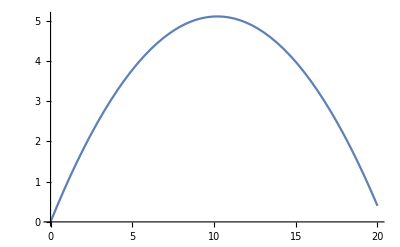

```mathematica
Plot[-0.049 x^2+x,{x,0,20}]
```

Mathematicaで数式処理で厳密解を求める.

```mathematica
parabola=DSolve[{x''[t]==0,y''[t]==-9.8,x[0]==y[0]==0,x'[0]==y'[0]==10},{x,y},t]
```

{{x→Function[{t},10. t],y→Function[{t},10. t-4.9 t^2]}}

```mathematica
Evaluate[{x[1],y[1]}/.First[parabola]]
```

{10.,5.1}

```mathematica
Plot[Evaluate[y[t/10]/.First[parabola]],{t,0,20}]
```

-Graphics-

### 1.5 NDSolve関数を使って微分方程式を数値的に解く

```mathematica
parabolan=NDSolve[{x''[t]==0,y''[t]==-9.8,x[0]==0,y[0]==0,x'[0]==10,y'[0]==10},{x,y},{t,0,2}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

```mathematica
Evaluate[{x[1],y[1]}/.First[parabolan]]
```

{10.,5.1}

```mathematica
Plot[Evaluate[y[t/10]/.First[parabolan]],{t,0,20}]
```

-Graphics-

#### 値の座標をアニメーション表示する.

```mathematica
DynamicModule[{x1,y1,n},Animate[{x1,y1}=Evaluate[{x[t],y[t]}/.First[parabolan]];
Show[Graphics[{Red,PointSize[.05],Point[{x1,y1}]}],
Plot[-0.049 x^2+x,{x,0,20}],
Axes->True,AspectRatio->1,PlotRange->{{0,22},{0,7}}],{t,0,2},AnimationRunning->False]]
```

## 2. 単振り子の運動方程式

棒の先に重り(質点)をぶら下げて他の端を固定する. 重りを横に動かして放すと往復運動を始める.
この運動を微分方程式を解くことでシミュレーションする.
ここでは, 長さ1の棒の固定端を原点にし, 鉛直方向からの偏角 (2 π)/3 または偏角 π/6 の位置で静止している状態を初期状態とする.

### 2.1 アニメーションの準備

振り子の状態を描画するアニメーションを準備する.
ここでは, パラメータ t を鉛直方向, すなわち, y軸の負の方向からの偏角として, 
0 度から360度までスライダーで動かせるようにしている.
また, 棒の長さを1としている. 偏角が s1 ラジアンのとき, 
質点の座標は (x1, y1) = (Sin[s1], -Cos[s1]) となる.

```mathematica
DynamicModule[{s1,x1,y1},Animate[s1=t/360*2π;x1=Sin[s1];y1=-Cos[s1];
Show[Graphics[{Purple,Line[{{0,0},{x1,y1}}]}],Graphics[{Red,PointSize[0.05],Point[{x1,y1}]}],Axes->True,Ticks->None,AspectRatio->1,PlotRange->{{-1.5,1.5},{-1.5,1.5}}],{t,0,360},AnimationRunning-> False]]
```

### 2.2 ラグランジアン (L1)

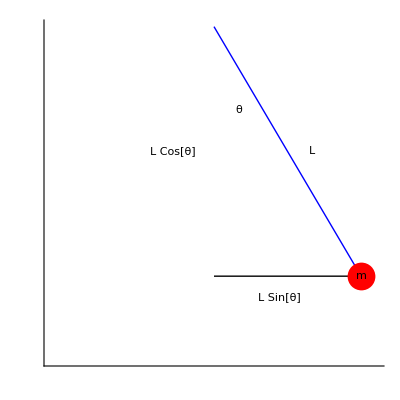

```mathematica
Block[{x1,y1},
x1=0.9;y1=-0.6;
Show[Graphics[{Blue,Line[{{0,0}, {x1,y1}}]}],
Graphics[{Black,Line[{{0,y1}, {x1,y1}}]}],Graphics[{Red,PointSize[.05],Point[{x1,y1}]}],Graphics[{Text["m",{x1,y1}],Text[θ,{ .15,-0.2}],Text["L",{0.6,-0.3}],
Text["L Cos[θ]",{-0.25,-0.3}],
 Text["L Sin[θ]",{0.4,-0.65}]}],
Axes->True,Ticks->None,AspectRatio->1,PlotRange->{{-1.0,1.0},{-0.8,0}}]]
```

弦の長さを L , 質点の質量を m, 位置を(x[t],y[t]), 速度を v=(x'[t],y'[t])とする.
弦とy軸とのなす角をθ=s[t]とすると, x[t]=L sin(s[t]), y[t]=- L cos(s[t])である.
また, x'[t]=L cos(s[t]) s'[t], 
y'[t]=-L sin(s[t]) s'[t]であることと,
cos(θ)^2+sin(θ)^2=1 に注意すると.
運動エネルギーは,
 E=1/2 m v^2=1/2 m(x'[t]^2+y'[t]^2)=1/2 m(L^2 cos(s[t])^2 s'[t]^2+L^2 sin(s[t])^2 s'[t]^2)=1/2 m L^2(s'[t])^2
位置エネルギーは, U= m g y[t] =-m g L cos(s[t])である.
ラグランジアンは,  L = E -U =1/2 m L^2(s'[t])^2+m g L cos(s[t])となる.
(ここで, g は, 重力加速度 9.8 m / sec^2 である.)

棒の長さ(l), 質点の質量 (m) と重力加速度 (g) の値を与えたときのラグランジアンを返す関数 L1[l, m,  g] を定義する.

```mathematica
L1[l_,m_,g_]:=1/2 m*l*l*s'[t]^2+m*g*l*Cos[s[t]]
```

### 2.3 ラグランジュの運動方程式

ラグランジュの運動方程式は次の式である.
ⅆ/ⅆt((∂L)/(∂s'))-(∂L)/(∂s)=0

#### 弦の長さ10, 質量 10, 弦重力加速度 9.8 のラグランジアンを lex1に代入しておく.

```mathematica
lex1=L1[10,10,9.8]
```

980. Cos[s[t]]+500 s'[t]^2

#### ラグランジュの運動方程式の計算

```mathematica
D[D[lex1,s'[t]],t]-D[lex1,s[t]]==0
```

980. Sin[s[t]]+1000 s''[t]==0

すなわち, s''[t] = - 0.98 Sin[s[t]] となります.

### 2.4 厳密解

#### 問題 2. 微分方程式 s''[t] = - 0.98 Sin[ s[t] ] について, (1) s[t]が小さいと仮定し, Sin[s[t]]≈s[t] と仮定した場合の一般解を求めよ. (2) 初期位置 s[0] = π/6, 初期速度 s'[0] = 0 とするとき, 周期を求めよ. (3:発展課題) s[t]が小さいとは限らない場合の一般解をヤコビの楕円関数を使って求めよ.

```mathematica
(1)DSolve[{s''[t]==-0.98s[t]},s,t]
```

{{s→Function[{t},1. C[1] Cos[0.989949 t]+1. C[2] Sin[0.989949 t]]}}

```mathematica
(2)上式に,s[0]=π/6,s'[0]=0を代入すると,C[1]=π/6,C[2]=0が得られる.よって特解s[t]=π/6 Cos[0.989949t]が得られる．この周期は2πである.
```

微分方程式の厳密解をDSolve関数で求める(初期角度 (2π)/3 の場合).

```mathematica
pendulum=DSolve[{s''[t]==-0.98 s[t],s[0]==2π/3,s'[0]==0},s,t]
```

{{s→Function[{t},2.0944 Cos[0.989949 t]]}}

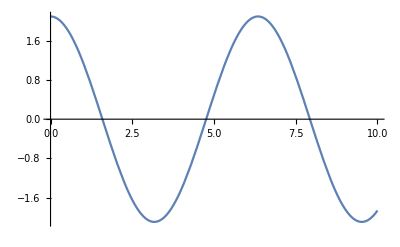

```mathematica
Plot[Evaluate[s[t]/.First[pendulum]],{t,0,10}]
```

```mathematica
pendulum=DSolve[{D[D[L1[10,10,9.8],s'[t]],t]-D[L1[10,10,9.8],s[t]]==0/.Sin[s[t]]->s[t],s[0]==2π/3,s'[0]==0},s,t]
```

{{s→Function[{t},2.0944 Cos[0.989949 t]]}}

```mathematica
pendulum=DSolve[{s''[t]==-0.98 s[t],s[0]==2π/3,s'[0]==0},s,t]
```

{{s→Function[{t},2.0944 Cos[0.989949 t]]}}

```mathematica
DSolve[s''[t]==-0.98 Sin[s[t]],s,t]
```

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

{{s→Function[{t},-2. JacobiAmplitude[0.5 √(1.96 t^2+t^2 C[1]+3.92 t C[2]+2. t C[1] C[2]+1.96 C[2]^2+C[1] C[2]^2),3.92/(1.96+C[1])]]},{s→Function[{t},2. JacobiAmplitude[0.5 √(1.96 t^2+t^2 C[1]+3.92 t C[2]+2. t C[1] C[2]+1.96 C[2]^2+C[1] C[2]^2),3.92/(1.96+C[1])]]}}

```mathematica
pend1=DSolve[D[D[L1[10,10,9.8],s'[t]],t]-D[L1[10,10,9.8],s[t]]==0,s,t]
```

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

{{s→Function[{t},-2. JacobiAmplitude[0.5 √(1.96 t^2+t^2 C[1]+3.92 t C[2]+2. t C[1] C[2]+1.96 C[2]^2+C[1] C[2]^2),3.92/(1.96+C[1])]]},{s→Function[{t},2. JacobiAmplitude[0.5 √(1.96 t^2+t^2 C[1]+3.92 t C[2]+2. t C[1] C[2]+1.96 C[2]^2+C[1] C[2]^2),3.92/(1.96+C[1])]]}}

```mathematica
Solve[{Evaluate[s[0]/.First[pend1]]==2π/3,Evaluate[s'[0]/.First[pend1]]==0},{C[1],C[2]}]
```

Solve::inex: Solveは厳密でない係数を持つ系または系に存在する厳密でない数値の直接有理化により得られた系を解くことができませんでした．Solveが用いるメソッドの多くは厳密な入力を必要とするため，Solveに厳密な系を指定した方がよいことがあります．

Solve[{-2. JacobiAmplitude[0.5 √(0.+1.96 C[2]^2+C[1] C[2]^2),3.92/(1.96+C[1])]==(2 π)/3,-((0.5 (0.+3.92 C[2]+2. C[1] C[2]) JacobiDN[0.5 √(0.+1.96 C[2]^2+C[1] C[2]^2),3.92/(1.96+C[1])])/(√(0.+1.96 C[2]^2+C[1] C[2]^2)))==0},{C[1],C[2]}]

NDSolve関数を使って微分方程式を数値的に解く(初期角度 (2π)/3 の場合).

```mathematica
pendulumn=NDSolve[{s''[t]==-0.98 Sin[s[t]],s[0]==2π/3,s'[0]==0},s,{t,0,100}];
```

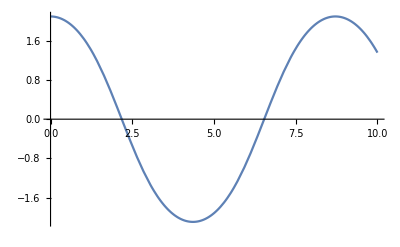

```mathematica
Plot[Evaluate[s[t]/.First[pendulumn]],{t,0,10}]
```

2 つのグラフを比べると明らかに異なる! 方程式を解けるように簡約したのが失敗!

微分方程式の厳密解をDSolve関数で求める(初期角度 π/6 の場合).

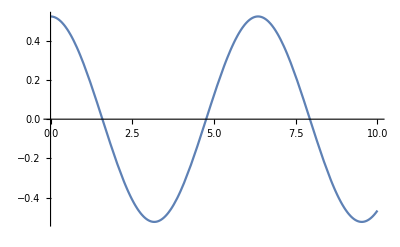

```mathematica
pendulum2=DSolve[{s''[t]==-0.98 s[t],s[0]==π/6,s'[0]==0},s,t];
Plot[Evaluate[s[t]/.First[pendulum2]],{t,0,10}]
```

NDSolve関数を使って微分方程式を数値的に解く(初期角度 π/6 の場合).

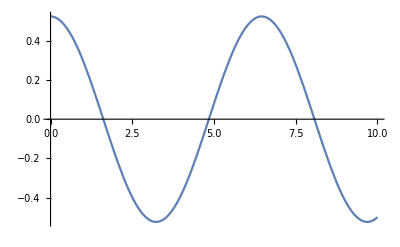

```mathematica
pendulumn2=NDSolve[{s''[t]==-0.98 Sin[s[t]],s[0]==π/6,s'[0]==0},s,{t,0,100}];
Plot[Evaluate[s[t]/.First[pendulumn2]],{t,0,10}]
```

初期角度が小さければ振れ幅は小さく, 簡約した微分方程式と解が似ている.

簡約しない微分方程式はDSolve関数では完全には解けない. 紙と鉛筆で楕円関数を用いて解いてみよう!

```mathematica
DSolve[{s''[t]==-0.98 Sin[s[t]]},s,t]
```

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

{{s→Function[{t},-2. JacobiAmplitude[0.5 √(1.96 t^2+t^2 C[1]+3.92 t C[2]+2. t C[1] C[2]+1.96 C[2]^2+C[1] C[2]^2),3.92/(1.96+C[1])]]},{s→Function[{t},2. JacobiAmplitude[0.5 √(1.96 t^2+t^2 C[1]+3.92 t C[2]+2. t C[1] C[2]+1.96 C[2]^2+C[1] C[2]^2),3.92/(1.96+C[1])]]}}

### 2.5 アニメーション表示

```mathematica
DynamicModule[{s1,x1,y1},Animate[s1=Evaluate[s[t]/.First[pendulumn]];x1=Sin[s1];y1=-Cos[s1];
Show[Graphics[{Purple,Line[{{0,0},{x1,y1}}]}],Graphics[{Red,PointSize[0.05],Point[{x1,y1}]}],Axes->True,Ticks->None,AspectRatio->1,PlotRange->{{-1.5,1.5},{-1.5,1.5}}],{t,1,100},AnimationRunning-> False,AnimationRate->10]]
```

## 3. バネの運動方程式

摩擦のない平面上に横に置いたバネの片方の端に重り (質点) をつなぎ
もう片方の端を壁に固定する. 重りを横に動かして放すと左右の振動を始める.
 この運動を微分方程式を解くことでシミュレーションする.
ここでは, 長さ10 cm のバネの固定端を原点にし, 重りの初期位置を15する.
また, バネ定数の値は 10 N/cm とする.

### 3.1 アニメーションの準備

バネの延び縮みに伴う質点の運動を表示するためのアニメーション画面を準備する.
下の例では, ボールを赤丸で表示し, そのx座標に変数x1を使っている.
 x1の値は, 0 から30までの間でスライダーで可変可能である.
初期位置を x1 = 10 としている.

```mathematica
DynamicModule[{x1},
Animate[
Show[
Graphics[{Red,PointSize[0.05],Point[{x1,0.15}]}],
Graphics[{Purple,Dashed,Arrowheads[{-.05,.05},],Arrow[{{0.0,0.15},{x1,0.15}}]}],
Axes->True,AspectRatio->0.2,PlotRange->{{0,30},{0,1.0}}],{x1,0,30},
Initialization:>{x1=10},
AnimationRunning-> False]]
```

### 3.2 ラグランジアン (L2)

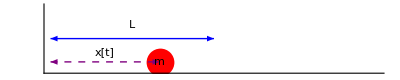

```mathematica
Show[
Graphics[{Red,PointSize[0.05],Point[{10,0.15}]}],
Graphics[{Purple,Dashed,Arrowheads[{-.05,.05},],Arrow[{{0.0,0.15},{10,0.15}}]}],
Graphics[{Blue,Arrowheads[{-.05,.05},],Arrow[{{0,0.5},{15,0.5}}]}],
Graphics[{Text["m",{10,0.15}],Text["L",{7.5,0.7}],
Text["x[t]",{5,0.3}]}],
Axes->True,Ticks->None,AspectRatio->0.2,PlotRange->{{0,30},{0,1.0}}]
```

負荷のかかっていないバネの長さを L , 質点の質量を m, 位置を x[t](cm), 速度を v=x'[t](cm/s)とする.
運動エネルギーは,
 E=1/2 m v^2=1/2 m(x'[t])^2
位置エネルギーは, U= 1/2 k(L-x[t])^2 である.
ラグランジアンは,  L = E -U =1/2 m(x'[t])^2-1/2 k(L-x[t])^2 となる.
(ここで, k は, バネ定数 (N/cm)である.)

バネの長さ(l), 質点の質量 (m) とバネ定数(k) の値を与えたときのラグランジアンを返す関数 L2[l, m,  k] を定義する.

```mathematica
L2[l_,m_,k_]:=1/2 m*(x'[t])^2-1/2 k*(l-x[t])^2
```

```mathematica
spring=NDSolve[{D[D[L2[10,10,10],x'[t]],t]-D[L2[10,10,10],x[t]]==0,x[0]==15,x'[0]==0},{x},{t,0,100}];
```

```mathematica
DynamicModule[{x1},
Animate[x1=Evaluate[x[t]/.First[spring]];
Show[
Graphics[{Red,PointSize[0.05],Point[{x1,0.15}]}],
Graphics[{Purple,Dashed,Arrowheads[{-.05,.05}],Arrow[{{0.0,0.15},{x1,0.15}}]}],
Axes->True,AspectRatio->0.2,PlotRange->{{0,30},{0,1.0}}],{t,0,100},
AnimationRunning-> False]]
```

```mathematica
DSolve[{D[D[L2[10,10,10],x'[t]],t]-D[L2[10,10,10],x[t]]==0,x[0]==15,x'[0]==0},x,t]
```

{{x→Function[{t},5 (2+Cos[t])]}}

#### 問題 3. (1) ラグランジアン(L2)から, ラグランジュの運動方程式(x[t] の満たす微分方程式)を簡単な形で求めなさい (2) 厳密解を紙と鉛筆, または, DSolve関数で求めなさい. (3) 初期位置 x[0]=20 のときのアニメーションを作成しなさい. (4) (t,x[t])の軌跡, すなわち, y=x[t] のグラフをPlot関数で表示しなさい.

## 4. 連接バネの運動方程式

摩擦のない平面上に横に置いたバネ2本を連接し, その中心と片方の先端に重り (質点) をつなぎ
もう片方の端を壁に固定する. 重りを横に動かして放すと左右の振動を始める.
 この運動を微分方程式を解くことでシミュレーションする.
ここでは, 長さ10 cm のバネを2本準備し固定端を原点にし連接する, 重りの長さは無視出来るとする.
また, バネ定数の値は 10 N/cm とする.

```mathematica
DynamicModule[{s1,s2},
Animate[
Show[
Graphics[{Black,Line[{{30,0},{30,2.0}}]}],
Graphics[{Black,Line[{{0,0},{0,2.0}}]}],
Graphics[{Blue,PointSize[0.05],Point[{s2,0.15}]}],Graphics[{Red,PointSize[0.05],Point[{s1,0.15}]}],
Graphics[{Purple,Dashed,Arrowheads[{-.05,.05},],Arrow[{{0.0,0.15},{s1,0.15}}]}],Graphics[{Purple,Dashed,Arrowheads[{-.05,.05}],Arrow[{{s1,0.15},{s2,0.15}}]}],
Axes->True,Ticks->None,AspectRatio->0.2,PlotRange->{{0,30},{0,1.0}}],{s1,0,30},{s2,0,30},
Initialization:>{s1=10;s2=20},
AnimationRunning-> False]]
```

ラグランジアン (L3)

```mathematica
L3[m_,l_,k_]:=1/2 m x1'[t]^2+1/2 m x2'[t]^2-1/2(k(l-x1[t])^2+k(l-(x2[t]-x1[t]))^2)
```

```mathematica
L3[10,10,10]
```

1/2 (-10 (10-x1[t])^2-10 (10+x1[t]-x2[t])^2)+5 x1'[t]^2+5 x2'[t]^2

```mathematica
Simplify[D[D[L3[10,10,10],x1'[t]],t]-D[L3[10,10,10],x1[t]]==0]
```

2 x1[t]+x1''[t]==x2[t]

```mathematica
Simplify[D[D[L3[10,10,10],x2'[t]],t]-D[L3[10,10,10],x2[t]]==0]
```

10+x1[t]==x2[t]+x2''[t]

```mathematica
doublespring=NDSolve[{4 x1[t]+x1''[t]==2 x2[t],20+2 x1[t]==2 x2[t]+x2''[t],x1[0]==5,x2[0]==20,x1'[0]==x2'[0]==0},{x1,x2},{t,0,100}];
```

```mathematica
DynamicModule[{s1,s2},
Animate[{s1,s2}=Evaluate[{x1[t],x2[t]}/.First[doublespring]];
Show[
Graphics[{Black,Line[{{30,0},{30,2.0}}]}],
Graphics[{Black,Line[{{0,0},{0,2.0}}]}],
Graphics[{Blue,PointSize[0.05],Point[{s2,0.15}]}],Graphics[{Red,PointSize[0.05],Point[{s1,0.15}]}],
Graphics[{Purple,Dashed,Arrowheads[{-.05,.05}],Arrow[{{0.0,0.15},{s1,0.15}}]}],Graphics[{Purple,Dashed,Arrowheads[{-.05,.05}],Arrow[{{s1,0.15},{s2,0.15}}]}],
Axes->True,Ticks->None,AspectRatio->0.2,PlotRange->{{0,30},{0,1.0}}],{t,0,100},
AnimationRunning-> False]]
```

#### 問題 4. 3本の連接したバネが両端の壁に固定されている場合のラグランジアン(L4)を求めシミュレーションを行いなさい.

#### アニメーションの準備

```mathematica
DynamicModule[{s1,s2},
Animate[
Show[
Graphics[{Black,Line[{{30,0},{30,2.0}}]}],
Graphics[{Black,Line[{{0,0},{0,2.0}}]}],
Graphics[{Blue,PointSize[0.05],Point[{s2,0.15}]}],Graphics[{Red,PointSize[0.05],Point[{s1,0.15}]}],
Graphics[{Purple,Dashed,Arrowheads[{-.05,.05},],Arrow[{{0.0,0.15},{s1,0.15}}]}],Graphics[{Purple,Dashed,Arrowheads[{-.05,.05}],Arrow[{{s1,0.15},{s2,0.15}}]}],Graphics[{Purple,Dashed,Arrowheads[{-.05,.05}],Arrow[{{s2,0.15},{30,0.15}}]}],
Axes->True,Ticks->None,AspectRatio->0.2,PlotRange->{{0,30},{0,1.0}}],{s1,0,30},{s2,0,30},
Initialization:>{s1=10;s2=20},
AnimationRunning-> False]]
```

## 5. 発展課題 (二重振り子のシミュレーション)

参考ムービー  →  http : // youtu.be/eo8VaXSLeyU

#### 問題 5. 連接振り子のラグランジアン(L5)を求めシミュレーションを行いなさい.

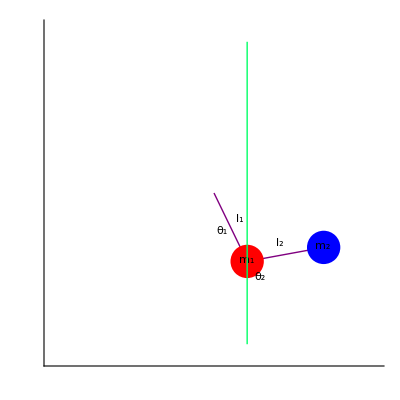

```mathematica
Block[{x1,y1,x2,y2},
x1=0.426024;y1=-0.904712;x2=1.40871;y2=-0.719444;
Show[Graphics[{Purple,Line[{{x1,y1}, {x2,y2}}]}],Graphics[{Blue,PointSize[.06],Point[{x2,y2}]}],Graphics[{Purple,Line[{{0,0}, {x1,y1}}]}],Graphics[{Red,PointSize[.06],Point[{x1,y1}]}],Graphics[{Text["m_1",{0.417078,-0.881541}],Text["m_2",{1.39758,-0.697567}],{Hue[.4],Line[{{x1,-2},{x1,2}}]},Text[Subscript[θ, 1],{ .1,-0.5}],Text[Subscript[θ, 2],{0.59269,-1.11151}],Text["l_1",{0.329272,-0.344951}],Text["l_2",{0.841473,-0.666905}]}],Axes->True,Ticks->None,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.2,2.2}}]]
```

#### アニメーションの準備

```mathematica
DynamicModule[{ss1,ss2,x1,x2,y1,y2},Animate[x1=Sin[ss1];y1=-Cos[ss1];
x2=Sin[ss1]+Sin[ss2];
y2=-Cos[ss1]-Cos[ss2];Show[Graphics[{Purple,Line[{{x1,y1},{x2,y2}}]}],Graphics[{Blue,PointSize[0.05],Point[{x2,y2}]}],Graphics[{Purple,Line[{{0,0},{x1,y1}}]}],Graphics[{Red,PointSize[0.05],Point[{x1,y1}]}],Axes->True,Ticks->None,AspectRatio->1,PlotRange->{{-2.5,2.5},{-2.5,2.5}}],{ss1,-π,π},{ss2,-π,π},AnimationRunning-> False]]
```

#### ラグランジアン (L5)

```mathematica
L5[g_,l_]:=1/2*l*l*(2(s1'[t])^2+(s2'[t])^2+2(s1'[t])(s2'[t])Cos[s1[t]-s2[t]])+g*l*(2 Cos[s1[t]]+Cos[s2[t]])
```

## 6. 課題提出方法

練習問題1,2,3,4,5について, 自分で出来る範囲で, Mathematicaのノートブックで解答を作成する.
完成したノートブックファイルをMoodleの課題欄に添付ファイルとして提出する.

## 7. (おまけ) シミュレーション結果を動画ファイルに保存する.

Mathematica には画像のリストを動画ファイルとして保存する関数Exportがある.
ここでは, 2.6 節の単振り子のシミュレーションの結果を動画 (MOVファイル) に
保存する例を紹介する.
2.6 節の Animate関数を実行している部分において, DynamicModule を Module へ,
Animate を Table へ変更すると出力画像のリストが得られる.
動画は1秒間に15枚の画像を使うので, 20 秒間の動画作成には300枚で十分である.
従ってパラメータの範囲を {i, 1, 300} として, t=i/3 とする.
出来た画像のリストを Export 関数に渡す. ファイル名として, "Documents/sample.mov" 
を指定すると, [書類] フォルダ中に "sample.mov" が保存される.

(注意)  20 秒の動画の場合, MOV形式の動画ファイルは作成に5秒程度かかり大きさが約600KBになる.

```mathematica
(* 実行するときはコメント (* *) を外して下さい. *)
(* Clear[x1,x2];
doublespring=NDSolve[{4 x1[t]+x1''[t]==2 x2[t],20+2 x1[t]==2 x2[t]+x2''[t],x1[0]==5,x2[0]==20,x1'[0]==x2'[0]==0},{x1,x2},{t,0,100}];
Export["Documents/sample1.mov",Module[{s1,s2},Table[{s1,s2}=Evaluate[{x1[i/3],x2[i/3]}/.First[doublespring]];
Show[
Graphics[{Black,Line[{{30,0},{30,2.0}}]}],
Graphics[{Black,Line[{{0,0},{0,2.0}}]}],
Graphics[{Blue,PointSize[0.05],Point[{s2,0.15}]}],Graphics[{Red,PointSize[0.05],Point[{s1,0.15}]}],
Graphics[{Purple,Dashed,Arrowheads[{-.05,.05}],Arrow[{{0.0,0.15},{s1,0.15}}]}],Graphics[{Purple,Dashed,Arrowheads[{-.05,.05}],Arrow[{{s1,0.15},{s2,0.15}}]}],
Axes->True,Ticks->None,AspectRatio->0.2,PlotRange->{{0,30},{0,1.0}}],{i,0,300}]]]
*)
```